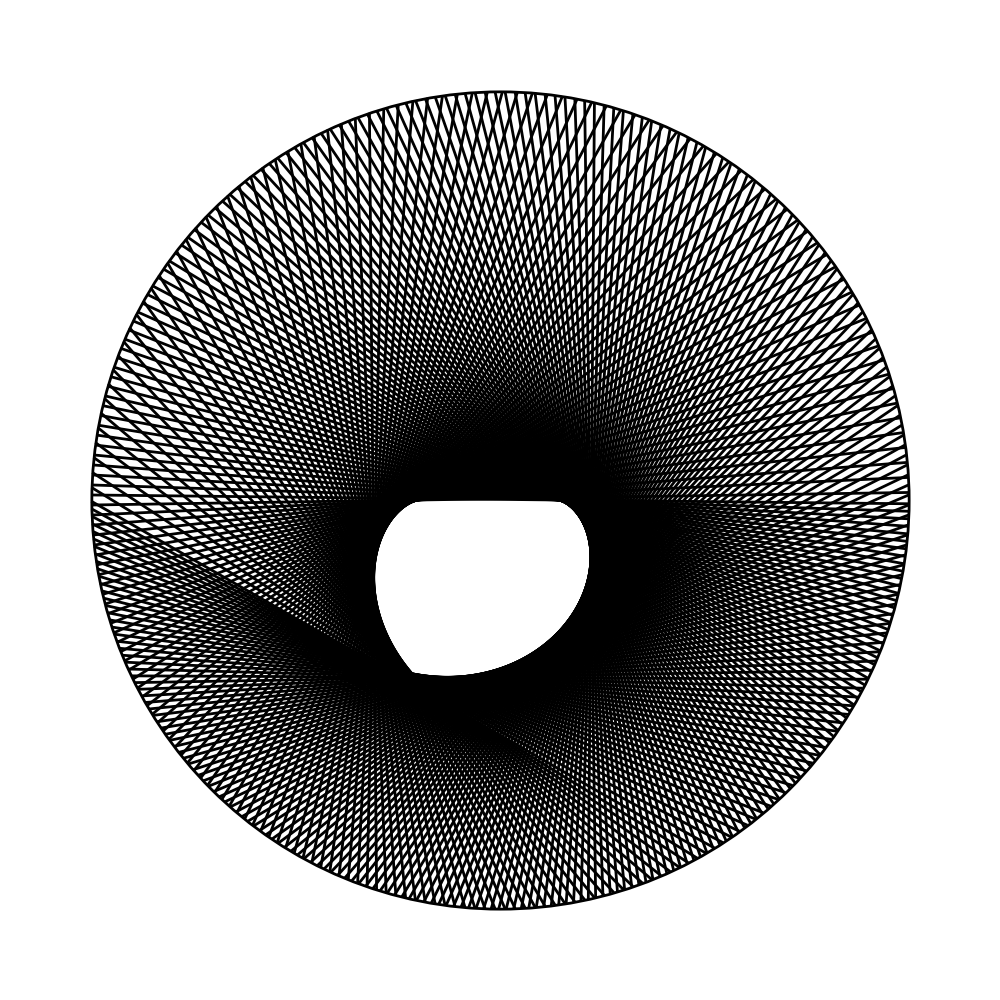

```mathematica
ClearAll["Global`*"];

r[t_]:=(
{(Sin[-t]),Cos[-t]}
);

fnfact[n_]:=n/(2^(Floor[Log[2,n]]+1)-2^Floor[Log[2,n]]);

line[from_,to_]:=(
Style[Line[{r[Pi/2+2Pi from],r[Pi/2+2Pi to]},VertexColors->{Red,Yellow}], Thickness[0.002]]
);

Graphics[{Table[line[fnfact[n], fnfact[n*3]],{n,513,1023,2}],Style[Circle[{0,0},1],Thickness[0.002]]},ImageSize->1000]
```